## Optical tweezer potential

[1] B. Saleh and M. Teich. Fundamentals of Photonics, 2nd edition.
[2] R. Grimm et al. Optical Dipole Traps for Neutral Atoms. Adv Atom Mol Opt Phy 42, 95-170 (2000).

z0: Rayleigh range
W: Beam width/radius
R: Wavefront radius of curvature
ζ: Gouy phase
ρ: Distance from tweezer axis
I0: Peak intensity

```mathematica
(*z0=(π W0^2)/λ;*)
z0=.
W=W0 √(1+(z/z0)^2);
R=z(1+(z0/z)^2);
ζ=ArcTan[z/z0];
intensity=2ϵ0 c I0 (W0/W)^2 Exp[-(2 ρ^2)/W^2]/.{ρ->dr W0,z->dax z0};
U=-1/(2ϵ0 c)Re[α]intensity/.Re[α]I0->U0
```

-(4 ⅇ^(-(2 dr^2)/(1+dax^2)))/(1+dax^2)

Defining dimensionless constants d_ax=z/z_0 and d_r=ρ/W_0

```mathematica
Ur=U/.dax->0;
Uax=U/.dr->0;
```

Spring constant in the axial and radial directions

```mathematica
kr=2(Normal[Series[Ur,{dr,0,2}]]+U0)/(W0^2 dr^2)
kax=2(Normal[Series[Uax,{dax,0,2}]]+U0)/(z0^2 dax^2)
```

16/W0^2

8/z0^2

```mathematica
ωr=√(kr/mNaCs);ωax=√(kax/mNaCs);
```

```mathematica
1/(2π)UnitConvert[ωr/.{U0->112 h MHz,mNaCs->ChemicalFormula["NaCs"]["MolecularMass"],W0->1.15 1064 nm}/.{h->Quantity["PlanckConstant"],MHz->Quantity["MHz"],nm->Quantity["nm"]}]
```

1.8972×10^-8 √kg m/s^2

```mathematica
Ur/.{U0->112 h MHz,mNaCs->ChemicalFormula["NaCs"]["MolecularMass"],W0->1.15 1064 nm}/.{h->Quantity["PlanckConstant"],MHz->Quantity["MHz"],nm->Quantity["nm"]}
```

-4 ⅇ^(-2 dr^2)

```mathematica
Ur
```

-4 ⅇ^(-2 dr^2)

## ND

```mathematica
ω=.;ℏ=1;U0=4;ω0=1;ω[t_]=ω0+.01 Cos[1 ω0 t];m=1;a=1;
```

```mathematica
p=-ⅈ ℏ D[#,x]&;
H=(p[p[#]]/(2m)+U0(1-ⅇ^(-(1/2 m ω[t]^2)/U0 x^2))#)&;
(*H=(p[p[#]]/(2m)+1/2 m ω[t]^2 x^2#)&;*)
```

```mathematica
SE=ⅈ D[ψ[x,t],t]==H[ψ[x,t]]/ℏ;
```

```mathematica
ψeig[n_,x_]:=1/(√(2^n n!))((m a ω0)/(π ℏ))^(1/4)Exp[-(m a ω0 x^2)/(2ℏ)]HermiteH[n,√((m a ω0)/ℏ)x]
```

```mathematica
SE
```

ⅈ ψ^(0,1)[x,t]==4 (1-ⅇ^(-1/8 x^2 (1+0.01 Cos[t])^2)) ψ[x,t]-1/2 ψ^(2,0)[x,t]

```mathematica
xmax=10;tmax=200;
schrodingerEq=-(1/2) D[ψ[x,t],{x,2}]+(1/2) x^2 ψ[x,t]==I D[ψ[x,t],t];
ψinit[x_]:=(1/π)^(1/4) Exp[-1/2 (x-1)^2];
sol=NDSolve[{SE,ψ[x,0]==ψeig[0,x],ψ[xmax,t]==0,ψ[-xmax,t]==0},ψ,{x,-xmax,xmax},{t,0,tmax},PrecisionGoal->10];
solution=ψ/. sol[[1]];
```

```mathematica
Manipulate[Plot[{Abs[solution[x,0]]^2,Abs[solution[x,t]]^2,U0(1-ⅇ^(-1/2(m ω0^2)/U0 x^2)),1/2 m ω0^2 x^2},{x,-xmax,xmax},PlotRange->{0,1},PlotStyle->{Dotted,Blue,Red,Purple},Filling->{2->Axis}],{t,0,tmax}]
```

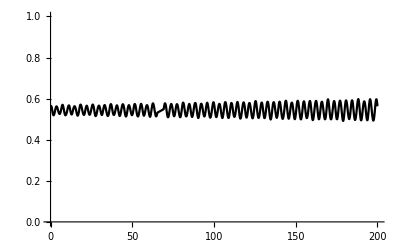

```mathematica
Plot[Abs[solution[0,t]]^2,{t,0,tmax},PlotRange->{0,1},PlotStyle->Black]
```